## Задание 1. Напишите функции, определяющие свойства полиэдра или его отношения с геометрическими объектами в пространстве. .

### Задание 1.1 Напишите функцию, вычисляющую список координат вершин i-той грани полиэдра. Выход – полигон, положительно ориентированный относительно внешней нормали, представленный списком Q= {q_1,q_2, ..., q_nGi, q_1} координат вершин i-той грани, при этом величина угла q_1 q_2 q_3 составляет менее 180 градусов. .

```mathematica
kmPolyhedronFaceToSurface[vertcoord_List,face_List]:=
Module[{P=Transpose@vertcoord,V,e1,e2,e3},
(* Параллельный перенос к началу координат *)
P[[face]]=(#-First@P[[face]])&/@P[[face]];
(* Векторы на ребрах полигона в старом базисе *)
V=(Most@#-Rest@#)&@P[[face]];
(* Построение нового базиса *)
{e1,e2}={First@V,First@Select[Rest@V,MatrixRank[{First@V,#}]>1&,1]};
(* Ортогонализация Грама и нормализация *)
{e1,e2}={e1,e2-e1.e2/e1.e1*e1};
{e1,e2}={e1/Norm@e1,e2/Norm@e2};
e3=Cross[e1,e2];
(* Координаты вершин грани в новом базисе *)
Take[#.Inverse[{e1,e2,e3}],2]&/@P[[face]]
]
```

```mathematica
kmGetPolyhedronFace[vertcoord_List,face_List]:=
Module[{F,l=Length@face,V=kmPolyhedronFaceToSurface[vertcoord,face],X,Y,pos},
F=Range[l]//Append[1];
(* Определение порядка обхода: если обход отрицательный, то грань отражаем симм. отн. X-оси (y -> -y) *)
X=Most[V[[All,1]]];Y=Most[V[[All,2]]];
If[Total@MapThread[Times,{Most@X,Rest@Y}]+X[[-1]]*Y[[1]]-Total@MapThread[Times,{Rest@X,Most@Y}]-X[[1]]*Y[[-1]]< 0,
V=V*ConstantArray[{1,-1},Length@V]];
(* Нахождение первого попавшегося угла, имеющего... *)
pos=First@First@Position[MapThread[List,{Take[F,{1,-3}],Take[F,{2,-2}],Take[F,{3,-1}]}],
x_/;If[x=== List,False,Det[{#2-#1,#3-#2}]&[Sequence@@V[[x]]]>0],1,1];
(* На выходе - грань при взгляде со стороны внешней нормали и номера вершин *)
{#,Transpose[vertcoord][[#]]}&@Take[Join[face,Rest@face],{pos,pos+l-1}]
];
```

Проверка :

```mathematica
P=Transpose@{{11,10,3},{10,25/2,5},{9,15,7},{-14,5,8},{-7,-5,-1},{-7.45,1,-2.35},{-7.9,7,-3.7},{-6,15,-10}};
G = {{1,2,3,4,5,1},{8,7,6,5,4,8},{1,5,6,7,1},{1,7,8,1},{1,8,3,2,1},{3,8,4,3}};
PT = Transpose@P;
PP= kmPolyhedronFaceToSurface[P,#]&/@G;
```

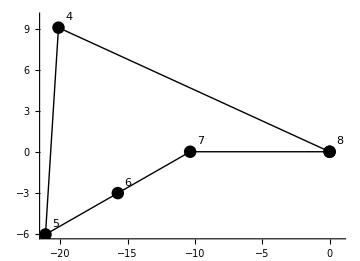
-Graphics- | -Graphics3D-

```mathematica
Grid[{{
Graphics[{PointSize-> 0.025,
Tooltip/@Point/@PP[[#]],Line@PP[[#]],
Sequence@@Table[Text[G[[#,i]],PP[[#,i]]+{0.75,0.75}],{i,1,Length@PP[[#]]-1}]},Axes-> True,ImageSize->Medium]&@2,
Graphics3D[{PointSize-> 0.025,
     Tooltip/@Point/@PT,
     Blue, Point@{-2,3,1},Black,
      Sequence@@Table[Line@PT[[G[[i]]]],{i,1,Length@G}],
      Sequence@@Table[Text[i,PT[[i]]+{0.75,0.75,0.75}],{i,1,Length@PT}]},Axes->True,ImageSize->Medium]}
}]
```

```mathematica
G[[2]]
kmPolyhedronFaceToSurface[P,G[[2]]]
kmGetPolyhedronFace[P,G[[2]]]
```

{8,7,6,5,4,8}

{{0.,0.},{-10.3586,4.44089×10^-16},{-15.7309,-3.027},{-21.1033,-6.054},{-20.1379,9.081},{0.,0.}}

{{6,5,4,8,7,6},{{-7.45,1,-2.35},{-7,-5,-1},{-14,5,8},{-6,15,-10},{-7.9,7,-3.7},{-7.45,1,-2.35}}}

### Задание 1.2 Напишите функцию, вычисляющую внешнюю нормаль к i-той грани полиэдра. Если грань представлена положительно ориентированной глядя с конца внешней нормали (обход вершин против часовой стрелки, при обходе область остается слева) и величина угла q_1 q_2 q_3 менее 180 градусов, то внешняя нормаль полиэдра к грани может быть вычислена как векторное произведение векторов N = V x W, где V= q_2-q_1, W = q_3- q_2, а точки q_1, q_2, q_3 - подряд идущие вершины грани полиэдра.

```mathematica
kmGetPolyhedronFaceNorm[{vertcoord_List,faces_List},i_Integer]:=Cross[#2-#1,#3-#2]&[Sequence@@Take[kmGetPolyhedronFace[vertcoord,faces[[i]]][[2]],3]]
```

Проверка :

```mathematica
n =kmGetPolyhedronFaceNorm[{P,G},2]; 
n=n/Norm@n
```

{-0.861096,-0.172219,-0.478387}

### Задание 1.4 Напишите тест-функцию ориентации точки относительно выпуклого полиэдра

```mathematica
kmPolyhedronPointPosConvex[{vertcoord_List,faces_List},p0_List]:=Not@ContainsAny[Sign@Table[(#.p0-#.Transpose[vertcoord][[faces[[i,1]]]])&@kmGetPolyhedronFaceNorm[{vertcoord,faces},i],{i,Length@faces}],{1}]
```

Проверка :

```mathematica
P1=Transpose@{{11,10,3},{10,25/2,5},{9,15,7},{-14,5,8},{-7,-5,-1},{-0.9,-3,-12.7},{-6,15,-10}};
G1 = {{1,2,3,4,5,1},{7,6,5,4,7},{1,5,6,1},{1,6,7,1},{1,7,3,2,1},{3,7,4,3}};
P1T = Transpose@P1;
PP1= kmPolyhedronFaceToSurface[P1,#]&/@G1;
```

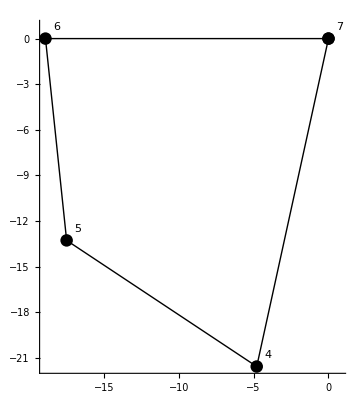
-Graphics- | -Graphics3D-

```mathematica
Grid[{{
Graphics[{PointSize-> 0.025,
Tooltip/@Point/@PP1[[#]],Line@PP1[[#]],
Sequence@@Table[Text[G1[[#,i]],PP1[[#,i]]+{0.75,0.75}],{i,1,Length@PP1[[#]]-1}]},Axes-> True,ImageSize->Medium]&@2,
Graphics3D[{PointSize-> 0.025,
     Tooltip/@Point/@P1T,
     Blue, Point@{4.5785758266795575,14.877211807262938,3.2888686434056007},Black,
      Sequence@@Table[Line@P1T[[G1[[i]]]],{i,1,Length@G1}],
      Sequence@@Table[Text[i,P1T[[i]]+{0.75,0.75,0.75}],{i,1,Length@P1T}]},Axes->True,ImageSize->Medium]}
}]
```

```mathematica
P0={1,7,-2}+8*{Random[],Random[],Random[]}
Print@kmPolyhedronPointPosConvex[{P1,G1},P0]
```

{1.99952,12.7811,-1.05568}

True

## Задание 2. Спроектируйте и постройте указанный в задании объект «Полиэдр». Напишите функции, создающие сфероидный или звездный объект. Визуализируйте результаты работы функций.

### Задание 2.4 Моделируйте каркасный сфероидный объект, двукратно надстраивая грани гексаэдра. Изобразите этапы моделирования и полученный объект.

```mathematica
kmHexaedroInit[]:={Transpose@{{0,0,1},{1,1,1},{1,0,0},{0,1,0}},{{1,3,2,1},{2,3,4,2},{1,4,3,1},{1,2,4,1}}};
```

```mathematica
kmHexaedroExpand[{vertcoord_List,faces_List}]:=
Module[{PT,G,p0,R, Phalf,Pnew,pn,p2n,Gnew,GNnew,dl,d,d2},
PT=Transpose@vertcoord; G=faces;
p0 = 1/Length[PT]*Total@PT;
R= Sqrt[#.#]&@(PT[[1]]-p0);
Do[
(* Надстройка i-ой грани *)
Phalf=MapThread[PT[[#1]]+1/2*(PT[[#2]]-PT[[#1]])&,{Most@G[[i]],Rest@G[[i]]}];
Pnew=p0+R*(#-p0)/Norm[#-p0]&/@Phalf;
pn=Most@G[[i]];
p2n=Range[Length@PT+1,Length@PT+Length@pn];
Gnew=p2n//Append[First@p2n];
GNnew=Join[#,{First@#}]&/@MapThread[List,{pn,p2n,Most[p2n]//Prepend[Last@p2n]}];
PT=Join[PT,Pnew];
G[[i]]=Gnew; 
G=Join[G,GNnew];
(* Поиск повторяющихся вершин и их удаление *)
dl=Length@DeleteDuplicates[PT];
While[Length@PT > dl,
d=First@First@Position[Tally@PT,y_/;If[y===List,False,Last@y>1],1,1];
d2=Last@Flatten@Position[PT,PT[[d]],1];
G=G/.{d2-> d};
G=G/.{x_/;x>d2->x-1};
PT=Delete[PT,d2];
]
,{i,1,Length@G}
];
(* Возврат результата (надстроенного гексаэдра)*)
{Transpose@PT,G}
]
```

```mathematica
kmHexaedroReduce[{vertcoord_List,faces_List}]:=
Module[{PT,G,Gnext, nP,nG},
PT=Transpose@vertcoord; G=faces;
(* Образование новых граней на месте удаления прежних *)
nP=If[Length@G>16,(Length@G-Length@PT-2)/2,4];
nG=If[Length@G>16,nP+2,4];
Gnext=Join[#,{First@#}]&/@Table[DeleteCases[DeleteDuplicates[Join@@Select[G,ContainsAny[#,{i}]&]],i],{i,1,nP}];
(* Удаление прежних граней и вершин, с ними связанных *)
G=Take[G,nG];
Do[
G=G/.{x_/;x>i->x-1};
Gnext=Gnext/.{x_/;x>i->x-1};
PT=Delete[PT,1]; 
,{i,Length@Gnext,1,-1}
];
(* Добавление новых граней *)
G=Join[G,Gnext];
(* Возврат результата (гексаэдра с обрезанными гранями)*)
{Transpose@PT,G}
]
```

```mathematica
{P2,G2}=kmHexaedroInit[];
```

```mathematica
{P2,G2}=kmHexaedroExpand[{P2,G2}];
```

```mathematica
{P2,G2}=kmHexaedroReduce[{P2,G2}];
```

```mathematica
P2T=Transpose@P2;
Graphics3D[{PointSize-> 0.025,
     Point/@P2T,
      Sequence@@Table[Line@P2T[[G2[[i]]]],{i,1,Length@G2}],
      Sequence@@Table[Text[i,P2T[[i]]+{0.05,0.05,0.05}],{i,1,Length@P2T}],
      Blue,(*Point@Take[P2T,12]*)
},Axes->True,ImageSize->Large]
```

-Graphics3D-

```mathematica
(*ClearAll["Global`*"]
```

```mathematica
(*Do[
p0={1/2,1/2,1/2};
R=Sqrt[3]/2;
Phalf=MapThread[P2T[[#1]]+1/2*(P2T[[#2]]-P2T[[#1]])&,{Most@G2[[iii]],Rest@G2[[iii]]}];
Pnew=p0+R*(#-p0)/Norm[#-p0]&/@Phalf;
l=Length@P2T;
pn=Most@G2[[iii]];
p2n=Range[l+1,l+Length@pn];
Gnew=p2n//Append[First@p2n];
GNnew=Join[#,{First@#}]&/@MapThread[List,{pn,p2n,Most[p2n]//Prepend[Last@p2n]}];
P2T=Join[P2T,Pnew];
G2[[iii]]=Gnew; 
G2=Join[G2,GNnew];

dl=Length@DeleteDuplicates[P2T];
While[Length@P2T > dl,
d=First@First@Position[Tally@P2T,y_/;If[y===List,False,Last@y>1],1,1];
d2=Last@Flatten@Position[P2T,P2T[[d]],1];
G2=G2/.{d2-> d};
G2=G2/.{x_/;x>d2->x-1};
P2T=Delete[P2T,d2];
]
,{iii,1,26}]*)
```

```mathematica
(*Gnext=Join[#,{First@#}]&/@Table[DeleteCases[DeleteDuplicates[Join@@Select[G2,ContainsAny[#,{i}]&]],i],{i,1,12}];
G2=Take[G2,14];
Do[
G2=G2/.{x_/;x>iii->x-1};
Gnext=Gnext/.{x_/;x>iii->x-1};
P2T=Delete[P2T,1]; 
,{iii,Length@Gnext,1,-1}];
G2=Join[G2,Gnext];*)
```

```mathematica
(*e1={-1,5/2,2};
e2={18,15,4};
ee1={-2/(3 √5),(√5)/3,4/(3 √5)};
ee2={23/(3 √70),(√(10/7))/3,-1/(3 √70)};
ee3={-1/(√14),√(2/7),-3/(√14)};*)
```

```mathematica
(*Graphics3D[{PointSize->0.025,Green,Point@{0,0,0},Blue,Point@ee1,Black,Point@e1,Line[{e1,{0,0,0},e2}],Blue, Line[{ee1,{0,0,0},ee2,{0,0,0},ee3}]}]*)
```

```mathematica
(*M1=-Norm[e1.e2/e1.e1*e1];
M2=Norm[e2-e1.e2/e1.e1*e1];
M1/(Norm[e1]*M2)*e1+1/M2*e2
{23/(3 √70),(√(10/7))/3,-1/(3 √70)}*)
```

```mathematica
(*kmPolyhedronFaceToSurface[vertcoord_List,face_List]:=
Module[{P=Transpose@vertcoord,V,e1,e2,e3,temp,proj},
(* Параллельный перенос к началу координат *)
P[[face]]=(#-First@P[[face]])&/@P[[face]];
(* Векторы на ребрах полигона в старом базисе *)
V=(Most@#-Rest@#)&@P[[face]];
(* Построение нового базиса *)
{e1,e2}={First@V,First@Select[Rest@V,MatrixRank[{First@V,#}]>1&,1]};
Print[e1.e2];
e3=Cross[e1,e2];
(* Координаты вершин грани в новом базисе *)
temp=Take[#.Inverse[{e1,e2,e3}],2]&/@P[[face]];
(* Переход к ортонормированному базису процессом Грама *)
proj = e1.e2/e1.e1*e1;
(* Координаты вершин грани в новом базисе *)
(#.Inverse[{{1/Norm@e1,0},{-Norm[proj]/(Norm[e1]*Norm[e2-proj]),1/Norm[e2-proj]}}])&/@temp
];*)
```